```mathematica
Clear["Global`*"]
```

Initialisierung von Matrix, Zuweisung der Eigenwerte

```mathematica
matBlock[ϕ_,ρ_,c11_,c12_,c44_,ω_,k_]:={{k^2*c11*Cos[ϕ]^2+k^2*c44*Sin[ϕ]^2-ρ*ω^2,k^2*(c12+c44)*Sin[ϕ]*Cos[ϕ]},{k^2*(c12+c44)*Sin[ϕ]*Cos[ϕ],k^2*c11*Sin[ϕ]^2+k^2*c44*Cos[ϕ]^2-ρ*ω^2}};
λ1[ϕ_,ρ_,c11_,c12_,c44_,ω_,k_]:=Assuming[k>0,FullSimplify[Eigenvalues[matBlock[ϕ,ρ,c11,c12,c44,ω,k]]]][[1]];
λ2[ϕ_,ρ_,c11_,c12_,c44_,ω_,k_]:=Assuming[k>0,FullSimplify[Eigenvalues[matBlock[ϕ,ρ,c11,c12,c44,ω,k]]]][[2]];
```

Berechnung der Frequenzen durch Bedingung, dass Eigenwerte gleich 0 sind

```mathematica
ω1[ϕ_,ρ_,c11_,c12_,c44_,k_]:=Assuming[k>0,FullSimplify[Values[Solve[λ1[ϕ,ρ,c11,c12,c44,ω,k]==0,ω]]]][[2]][[1]]
ω2[ϕ_,ρ_,c11_,c12_,c44_,k_]:=Assuming[k>0,FullSimplify[Values[Solve[λ2[ϕ,ρ,c11,c12,c44,ω,k]==0,ω]]]][[2]][[1]]
```

Berechnung der Geschwindigkeiten und Ausgabe dieser

```mathematica
v1[ϕ_,ρ_,c11_,c12_,c44_,k_]:=ω1[ϕ,ρ,c11,c12,c44,k]/k
v2[ϕ_,ρ_,c11_,c12_,c44_,k_]:=ω2[ϕ,ρ,c11,c12,c44,k]/k
```

```mathematica
v1[ϕ,ρ,c11,c12,c44,k]
v2[ϕ,ρ,c11,c12,c44,k]
```

(√(2 c11+2 c44-√2 √(c11^2+c12^2-2 c11 c44+2 c44 (c12+c44)+(c11+c12) (c11-c12-2 c44) Cos[4 ϕ])))/(2 √ρ)

(√(2 c11+2 c44+√2 √(c11^2+c12^2-2 c11 c44+2 c44 (c12+c44)+(c11+c12) (c11-c12-2 c44) Cos[4 ϕ])))/(2 √ρ)

Initialisierung der materialspezifischen Parameter

```mathematica
Subscript[ρ, Al]:=2.6795*10^3;
Subscript[ρ, Cu]=8.899*10^3;
Subscript[c11, Al]=1.068*10^11;
Subscript[c12, Al]=0.607*10^11;
Subscript[c44, Al]=0.282*10^11;
Subscript[c11, Cu]=1.684*10^11;
Subscript[c12, Cu]=1.214*10^11;
Subscript[c44, Cu]=0.754*10^11;
```

Polarplot für Aluminium:

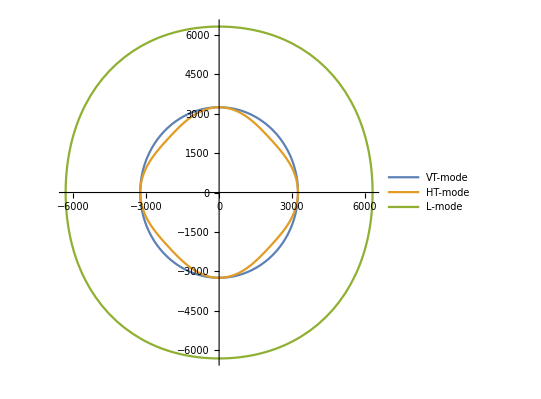

```mathematica
PolarPlot[{√(Subscript[c44, Al]/Subscript[ρ, Al]),v1[ϕ,Subscript[ρ, Al],Subscript[c11, Al],Subscript[c12, Al],Subscript[c44, Al],1],v2[ϕ,Subscript[ρ, Al],Subscript[c11, Al],Subscript[c12, Al],Subscript[c44, Al],1]},{ϕ,0,2 Pi}, PlotLegends->{"VT-mode","HT-mode","L-mode"}, PlotPoints->100]
```

Polarplot für Kupfer:

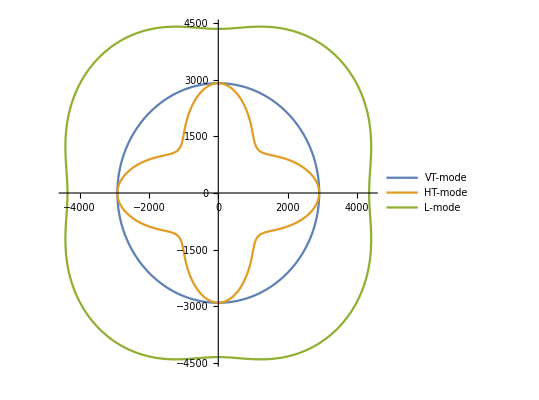

```mathematica
PolarPlot[{√(Subscript[c44, Cu]/Subscript[ρ, Cu]),v1[ϕ,Subscript[ρ, Cu],Subscript[c11, Cu],Subscript[c12, Cu],Subscript[c44, Cu],1],v2[ϕ,Subscript[ρ, Cu],Subscript[c11, Cu],Subscript[c12, Cu],Subscript[c44, Cu],1]},{ϕ,0,2 Pi}, PlotLegends->{"VT-mode","HT-mode","L-mode"}, PlotPoints->100]
```

Anisotropiefaktoren für Kupfer und Aluminium:

```mathematica
Subscript[a, Al]=(2*Subscript[c44, Al])/(Subscript[c11, Al]-Subscript[c12, Al])
Subscript[a, Cu]=(2*Subscript[c44, Cu])/(Subscript[c11, Cu]-Subscript[c12, Cu])
```

1.22343

3.20851

Aluminium Longitudinal sowie Max./Min-Werte

```mathematica
√(Subscript[c44, Al]/Subscript[ρ, Al])
v1[Pi/4,Subscript[ρ, Al],Subscript[c11, Al],Subscript[c12, Al],Subscript[c44, Al],1]
v2[0,Subscript[ρ, Al],Subscript[c11, Al],Subscript[c12, Al],Subscript[c44, Al],1]
v2[Pi/4,Subscript[ρ, Al],Subscript[c11, Al],Subscript[c12, Al],Subscript[c44, Al],1]
```

3244.13

2932.98

6313.33

6463.76

Kupfer Longitudinal sowie Max./Min-Werte

```mathematica
√(Subscript[c44, Cu]/Subscript[ρ, Cu])
v1[Pi/4,Subscript[ρ, Cu],Subscript[c11, Cu],Subscript[c12, Cu],Subscript[c44, Cu],1]
v2[0,Subscript[ρ, Cu],Subscript[c11, Cu],Subscript[c12, Cu],Subscript[c44, Cu],1]
v2[Pi/4,Subscript[ρ, Cu],Subscript[c11, Cu],Subscript[c12, Cu],Subscript[c44, Cu],1]
```

2910.82

1625.04

4350.11

4975.5